```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["SMatrix`", Path->ParentDirectory@NotebookDirectory[]]
Directory[]
```

C:\Users\marucha\Desktop\SMatrixBootstrap\pionScatteringResult

```mathematica
resultDirectories = FileNames["quartic_*_out"]
```

{quartic_coupling_imp_n_0_j_8.max.gz_out,quartic_coupling_imp_n_0_j_8.min.gz_out,quartic_coupling_imp_n_10_j_22.max.gz_out,quartic_coupling_imp_n_10_j_22.min.gz_out,quartic_coupling_imp_n_12_j_24.max.gz_out,quartic_coupling_imp_n_12_j_24.min.gz_out,quartic_coupling_imp_n_14_j_26.max.gz_out,quartic_coupling_imp_n_14_j_26.min.gz_out,quartic_coupling_imp_n_16_j_28.max.gz_out,quartic_coupling_imp_n_16_j_28.min.gz_out,quartic_coupling_imp_n_18_j_30.max.gz_out,quartic_coupling_imp_n_18_j_30.min.gz_out,quartic_coupling_imp_n_1_j_9.max.gz_out,quartic_coupling_imp_n_1_j_9.min.gz_out,quartic_coupling_imp_n_20_j_32.max.gz_out,quartic_coupling_imp_n_20_j_32.min.gz_out,quartic_coupling_imp_n_2_j_10.max.gz_out,quartic_coupling_imp_n_2_j_10.min.gz_out,quartic_coupling_imp_n_3_j_11.max.gz_out,quartic_coupling_imp_n_3_j_11.min.gz_out,quartic_coupling_imp_n_4_j_16.max.gz_out,quartic_coupling_imp_n_4_j_16.min.gz_out,quartic_coupling_imp_n_5_j_17.max.gz_out,quartic_coupling_imp_n_5_j_17.min.gz_out,quartic_coupling_imp_n_6_j_18.max.gz_out,quartic_coupling_imp_n_6_j_18.min.gz_out,quartic_coupling_imp_n_7_j_19.max.gz_out,quartic_coupling_imp_n_7_j_19.min.gz_out,quartic_coupling_imp_n_8_j_20.max.gz_out,quartic_coupling_imp_n_8_j_20.min.gz_out,quartic_coupling_imp_n_9_j_21.max.gz_out,quartic_coupling_imp_n_9_j_21.min.gz_out,quartic_coupling_n_10_j_20.max.gz_out,quartic_coupling_n_10_j_20.min.gz_out,quartic_coupling_n_10_j_22.max.gz_out,quartic_coupling_n_10_j_22.min.gz_out,quartic_coupling_n_12_j_24.max.gz_out,quartic_coupling_n_12_j_24.min.gz_out,quartic_coupling_n_14_j_26.max.gz_out,quartic_coupling_n_14_j_26.min.gz_out,quartic_coupling_n_16_j_28.max.gz_out,quartic_coupling_n_16_j_28.min.gz_out,quartic_coupling_n_18_j_30.max.gz_out,quartic_coupling_n_18_j_30.min.gz_out,quartic_coupling_n_20_j_32.max.gz_out,quartic_coupling_n_20_j_32.min.gz_out,quartic_coupling_n_2_j_14.max.gz_out,quartic_coupling_n_2_j_14.min.gz_out,quartic_coupling_n_3_j_15.max.gz_out,quartic_coupling_n_3_j_15.min.gz_out,quartic_coupling_n_4_j_16.max.gz_out,quartic_coupling_n_4_j_16.min.gz_out,quartic_coupling_n_5_j_17.max.gz_out,quartic_coupling_n_5_j_17.min.gz_out,quartic_coupling_n_6_j_18.max.gz_out,quartic_coupling_n_6_j_18.min.gz_out,quartic_coupling_n_7_j_19.max.gz_out,quartic_coupling_n_7_j_19.min.gz_out,quartic_coupling_n_8_j_20.max.gz_out,quartic_coupling_n_8_j_20.min.gz_out,quartic_coupling_n_9_j_21.max.gz_out,quartic_coupling_n_9_j_21.min.gz_out,quartic_coupling_with_pole_n_10_j_22.max.gz_out,quartic_coupling_with_pole_n_10_j_22.min.gz_out,quartic_coupling_with_pole_n_12_j_24.max.gz_out,quartic_coupling_with_pole_n_12_j_24.min.gz_out,quartic_coupling_with_pole_n_14_j_26.max.gz_out,quartic_coupling_with_pole_n_14_j_26.min.gz_out,quartic_coupling_with_pole_n_16_j_28.max.gz_out,quartic_coupling_with_pole_n_16_j_28.min.gz_out,quartic_coupling_with_pole_n_18_j_30.max.gz_out,quartic_coupling_with_pole_n_18_j_30.min.gz_out,quartic_coupling_with_pole_n_1_j_13.max.gz_out,quartic_coupling_with_pole_n_1_j_13.min.gz_out,quartic_coupling_with_pole_n_2_j_14.max.gz_out,quartic_coupling_with_pole_n_2_j_14.min.gz_out,quartic_coupling_with_pole_n_3_j_15.max.gz_out,quartic_coupling_with_pole_n_3_j_15.min.gz_out,quartic_coupling_with_pole_n_4_j_16.max.gz_out,quartic_coupling_with_pole_n_4_j_16.min.gz_out,quartic_coupling_with_pole_n_5_j_17.max.gz_out,quartic_coupling_with_pole_n_5_j_17.min.gz_out,quartic_coupling_with_pole_n_6_j_18.max.gz_out,quartic_coupling_with_pole_n_6_j_18.min.gz_out,quartic_coupling_with_pole_n_7_j_19.max.gz_out,quartic_coupling_with_pole_n_7_j_19.min.gz_out,quartic_coupling_with_pole_n_8_j_20.max.gz_out,quartic_coupling_with_pole_n_8_j_20.min.gz_out,quartic_coupling_with_pole_n_9_j_21.max.gz_out,quartic_coupling_with_pole_n_9_j_21.min.gz_out}

```mathematica
ParseFilename[name_]:=  StringCases[name,
"quartic_coupling_"~~variation:Longest[("imp_"|"with_pole_"|"")]~~"n_"~~n:NumberString~~"_j_"~~j:NumberString~~"."~~type:("max"|"min")~~".gz_out":><|"variation"->variation,"type"->type,"n"->ToExpression[n],"j"->ToExpression[j]|>]//First
```

```mathematica
LoadResults[directory_]:= Module[{keyfile = FileNameJoin[{"keys",StringDrop[directory,-10]<>"key.m"}]},
Join[ParseFilename[directory],LoadSDPBOutput[directory, keyfile]]
];
```

```mathematica
dataset = Select[KeyExistsQ["primalObjective"]][LoadResults/@resultDirectories]//Select[#terminateReason=="found primal-dual optimal solution"&];
Dataset[dataset]
```

Dataset[<>]

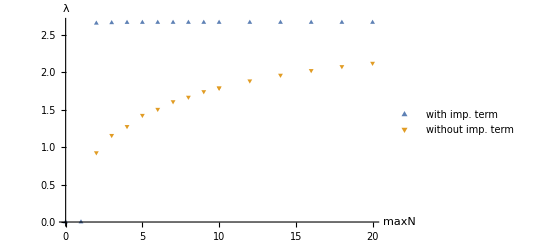

```mathematica
maxLambdaUnimproved = Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation==""&&#type=="max"&]];
maxLambdaImproved = Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="imp_"&&#type=="max"&]];
ListPlot[{maxLambdaImproved, maxLambdaUnimproved},PlotMarkers->{▲,▼},AxesLabel->{maxN, λ},PlotLegends->{"with imp. term", "without imp. term"}]
```

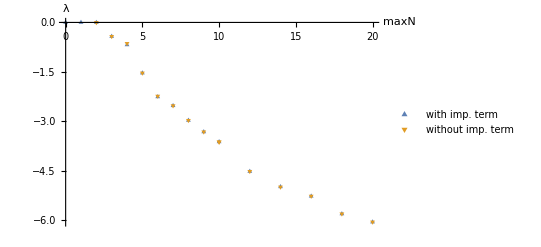

```mathematica
minLambdaUnimproved = Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation==""&&#type=="min"&]];
minLambdaImproved = Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="imp_"&&#type=="min"&]];
ListPlot[{minLambdaImproved, minLambdaUnimproved},PlotMarkers->{▲,▼},AxesLabel->{maxN, λ},PlotLegends->{"with imp. term", "without imp. term"}]
```

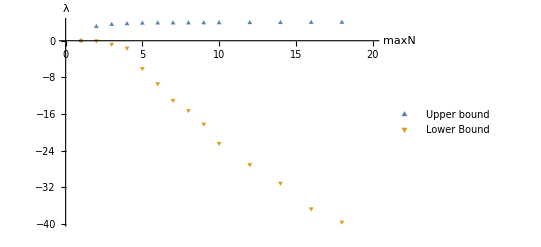

```mathematica
minLambdaWithCubic = Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="with_pole_"&&#type=="min"&]];
maxLambdaWithCubic = Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="with_pole_"&&#type=="max"&]];
ListPlot[{maxLambdaWithCubic, minLambdaWithCubic},PlotMarkers->{▲,▼},AxesLabel->{maxN, λ},PlotLegends->{"Upper bound", "Lower Bound"}, PlotRange->{{0,20}, Automatic}]
```

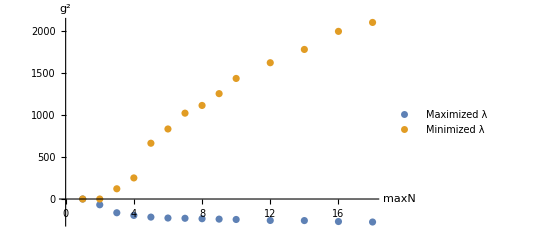

```mathematica
cubicGwithMinLambda = Map[{#n,#vector[g]}&,Select[dataset,#variation=="with_pole_"&&#type=="min"&]];
cubicGwithMaxLambda = Map[{#n,#vector[g]}&,Select[dataset,#variation=="with_pole_"&&#type=="max"&]];
ListPlot[{cubicGwithMaxLambda, cubicGwithMinLambda},AxesLabel->{maxN, g^2},PlotLegends->{"Maximized λ", "Minimized λ"}]
```

```mathematica
cubicResultDirectories = FileNames["cubic_*_out"]
```

{cubic_coupling_n_12_j_24.max.gz_out,cubic_coupling_n_14_j_26.max.gz_out,cubic_coupling_n_16_j_28.max.gz_out,cubic_coupling_n_18_j_30.max.gz_out,cubic_coupling_n_1_j_13.max.gz_out,cubic_coupling_n_2_j_14.max.gz_out,cubic_coupling_n_3_j_15.max.gz_out,cubic_coupling_n_4_j_16.max.gz_out,cubic_coupling_n_5_j_17.max.gz_out,cubic_coupling_n_6_j_18.max.gz_out,cubic_coupling_n_7_j_19.max.gz_out,cubic_coupling_n_8_j_20.max.gz_out,cubic_coupling_n_9_j_21.max.gz_out}

```mathematica
ParseCubicFilename[name_]:=  StringCases[name,
"cubic_coupling_"~~"n_"~~n:NumberString~~"_j_"~~j:NumberString~~"."~~type:("max"|"min")~~".gz_out":><|"type"->type,"n"->ToExpression[n],"j"->ToExpression[j]|>]//First
```

```mathematica
LoadCubicResults[directory_]:= Module[{keyfile = FileNameJoin[{"keys",StringDrop[directory,-10]<>"key.m"}]},
Join[ParseCubicFilename[directory],LoadSDPBOutput[directory, keyfile]]
];
```

```mathematica
cubicDataset = Select[KeyExistsQ["primalObjective"]][LoadCubicResults/@cubicResultDirectories]//Select[#terminateReason=="found primal-dual optimal solution"&];
Dataset[cubicDataset]
```

```mathematica
maxG = Map[{#n,Sqrt[#vector[g]]}&,cubicDataset];
```

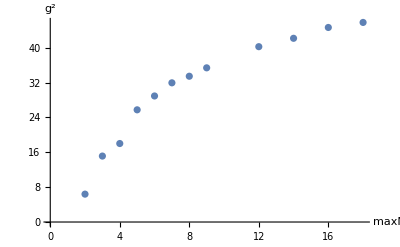

```mathematica
ListPlot[maxG,AxesLabel->{maxN, g^2}]
```

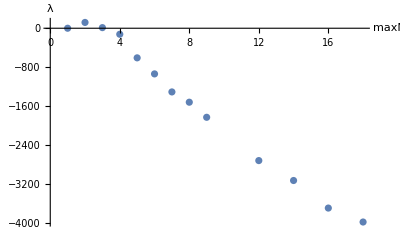

```mathematica
lambdaForMaxG = Map[{#n,#vector[α[0,0,0]]}&,cubicDataset];
ListPlot[lambdaForMaxG,AxesLabel->{maxN,λ}]
```